```mathematica
Location, Observer, Velocity, Triple CrossProduct, Integrand
```

```mathematica
r[t_]:=ρ{Cos[ω0 t],Sin[ω0 t],0}
n[θ_]:={Sin[θ],0,Cos[θ]}
β[t_]:=D[r[t],t]/c
tripleproduct[t_,θ_]:=Cross[n[θ],Cross[n[θ],β[t]]]
int[t_,θ_]:=tripleproduct[t,θ]*Exp[I ω (t-Dot[n[θ],r[t]]/c)]
```

```mathematica
Constants
```

```mathematica
ρ=100;
b=.9;
c=3*10^8;
ω0=(b c)/ρ;
T=(2Pi)/ω0;
ω=10^7;
```

```mathematica
γ=Sqrt[1-b^2]^-1;
ξ[θ_]:=(ω ρ)/(3 c)(γ^-2+θ^2)^(3/2);
```

```mathematica
Definitions of exact function (1) and Jackson's Approximation (2)
```

```mathematica
Jackson1[θ_,ω_]:=ω^2/(4 π^2)((Norm[NIntegrate[int[t,θ],{t,-T/2,T/2}]])^2)
Jackson2[θ_,ω_]:=1/(3 π^2)((ω ρ)/c)^2(γ^-2+θ^2)^2((BesselK[2/3,ξ[θ]])^2+θ^2/(γ^-2+θ^2)(BesselK[1/3,ξ[θ]])^2)
```

```mathematica
Comparison between (1) and (2) via logarithmic difference plot; the brighter the color the smaller the difference
```

```mathematica
ContourPlot[Log10[Jackson1[θ,ω]-Jackson2[θ-Pi/2,ω]],{θ,0,Pi},{ω,0,10ω0},PlotLegends->Automatic]
```

-Graphics-

```mathematica
Replacing the integrand with n × β and comparing via logarithmic difference plot
```

```mathematica
newint[t_,θ_]:=Cross[n[θ],β[t]]Exp[I ω (t-Dot[n[θ],r[t]]/c)]
Jackson3[θ_,ω_]:=ω^2/4((Norm[NIntegrate[newint[t,θ],{t,-T/2,T/2}]])^2)
```

```mathematica
ContourPlot[Log10[Jackson3[θ,ω]-Jackson1[θ,ω]],{θ,0,Pi},{ω,0,10ω0},PlotLegends->Automatic]
```

-Graphics-

```mathematica
Landau-Lifshitz result compared to Jackson's result
```

```mathematica
D[BesselJ[n,x],x]
```

1/2 (BesselJ[-1+n,x]-BesselJ[1+n,x])

```mathematica
landau1[θ_,n_]:=n^2(Tan[θ]^2 BesselJ[n,b n Cos[θ]]^2+b^2(1/2 (BesselJ[-1+n,b n Cos[θ]]-BesselJ[1+n,b n Cos[θ]]))^2)
```

```mathematica
ContourPlot[Log10[Jackson1[θ,ω]-landau1[θ-π/2,ω/ω0]],{θ,0,Pi},{ω,0,10*ω0},PlotLegends->Automatic]
```

-Graphics-

```mathematica
besselp[n_,y_]:=D[BesselJ[n,x],x]/.x->y
Landau[θ_,n_]:=n^2(Tan[θ]^2 BesselJ[n,b n Cos[θ]]^2+b^2 besselp[n,b n Cos[θ]]^2)
```

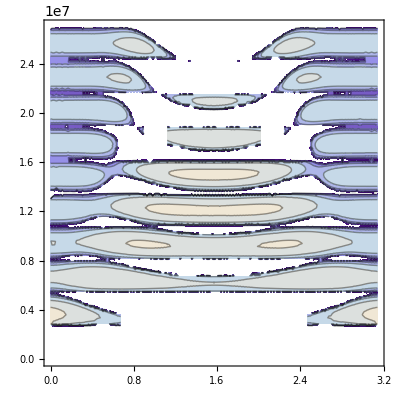

```mathematica
ContourPlot[Log10[Jackson1[θ,ω]-Landau[θ-π/2,ω/ω0]],{θ,0,Pi},{ω,0,10*ω0}]
```